```mathematica
ClearAll["Global`*"]
```

Import Data

```mathematica
data = Import[StringJoin[{"[YOUR FILE PATH]/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{"[YOUR FILE PATH]/data/carnivoredensities_trimmed.csv"}],"csv"];
ppmrfitdata = Import[StringJoin[{"[YOUR FILE PATH]/data/ppmr_fit_table_revreps.csv"}],"csv"];
```

Define consumer-resource system and mass-dependent parameters

```mathematica
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+bP+ξ)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->w*bP[M]};(*take σ*(1-R/k)=0 to take out starvation component*)
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R))+ρ)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->w*bP[M]};
LVSS = FullSimplify[Solve[{0==eqnC,0==eqnR},{C,R}]];
Csol = C/.LVSS[[3]]
Rsol = R/.LVSS[[3]]
```

-((α Y[M] (kRes (4 (ξ+w bP[M]-λ[M]+μ[M])^2 (ξ+w bP[M]+μ[M]+Y[M] ρ[M])+2 (5 w^2 bP[M]^2+2 λ[M]^2-5 λ[M] (ξ+μ[M])+(ξ+μ[M]) (5 (ξ+μ[M])+2 Y[M] ρ[M])+w bP[M] (-5 λ[M]+10 (ξ+μ[M])+2 Y[M] ρ[M])) σ[M]+(6 w bP[M]-2 λ[M]+6 (ξ+μ[M])+3 Y[M] ρ[M]) σ[M]^2)+2 ξ^2 √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))+4 w ξ bP[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))+2 w^2 bP[M]^2 √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))-2 ξ λ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))-2 w bP[M] λ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))+4 ξ μ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))+4 w bP[M] μ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))-2 λ[M] μ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))+2 μ[M]^2 √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))+2 ξ Y[M] ρ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))+2 w bP[M] Y[M] ρ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))-2 Y[M] λ[M] ρ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))+2 Y[M] μ[M] ρ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))+2 ξ σ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))+2 w bP[M] σ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))-2 λ[M] σ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))+2 μ[M] σ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))-Y[M] ρ[M] σ[M] √(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2))))/(4 σ[M]^2 (2 (λ[M]+Y[M] ρ[M]) (ξ+w bP[M]+μ[M]+Y[M] ρ[M])+(2 λ[M]+3 Y[M] ρ[M]) σ[M])))

(kRes (2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])+√(kRes^2 (8 σ[M] (ξ+w bP[M]+μ[M]+σ[M])+(2 (ξ+w bP[M]-λ[M]+μ[M])+σ[M])^2)))/(4 σ[M])

Define metabolic parameters for herbivore consumer and resource

```mathematica
kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
ρ[M_]:=B0*M^(η)/(M*Ed);
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)
```

Metabolic parameters for predator that eats herbivore consumer

```mathematica
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
```

Predator/prey interaction parameters

```mathematica
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)


(*--------------------*)
(*Optimal Predator mass given Prey (M) Mass*)
OptPredMass[M_]:=ppmrint*M^ppmrslope;
ppmrslope = (ppmrfitdata[[3,1]]);
ppmrint = Exp[(ppmrfitdata[[2,1]])]*((1/1000)^ppmrslope)*1000; (*converted from KG to grams*)

(*Inverse: Optimal Prey mass given Predator (Mp) Mass*)
OptPreyMass[Mp_]:=Evaluate[M/.Solve[OptPredMass[M]==Mp,M][[1]]];

(*--------------------*)



OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Calculate Herbivore Yield

```mathematica
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[M_]:=YHerbperRes[M];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
```

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?

```mathematica
CsolNoPred=Csol/.{bP[M]->0};
RsolNoPred=Rsol/.{bP[M]->0};
```

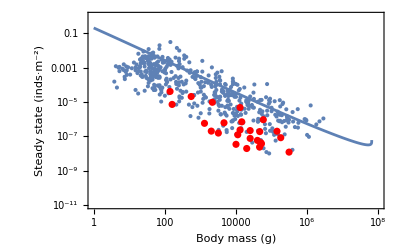

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5}],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*CsolNoPred/.{ξ->0,w->1},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]]
}]
```

Calculate Predator Yield

```mathematica
(*Yield of predator per prey*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
```

Calculate Consumer and Predator Boundary Densities

```mathematica
PreyDensityTheoreticalMax[M_] :=  Evaluate[YHerbperRes[M]*kRes//Simplify]; (*Grams Herb / m^2 given the mass of a predator and the optimal prey mass given predator mass conversion*)
PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[Ypred[Mp,M]*YHerbperRes[M]*kRes//Simplify];
```

Plot the Theoretical Maxima for herbivore consumers and predators relative to Damuth Data

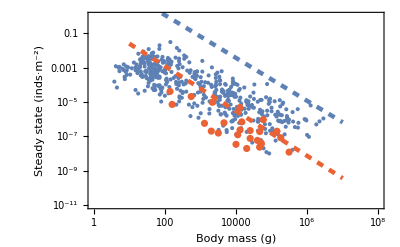

```mathematica
MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*PreyDensityTheoreticalMax[M],{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/M)*PredatorDensityTheoreticalMax[OptPredMass[M],M],{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]
```

```mathematica
Export[StringJoin[{"[YOUR FILE PATH]/fig_maxdensities.pdf"}],PredPlot,"PDF"]
```

Calculate per-capita Predation Mortality Rate as (predation rate per gram consumer)*(predated consumer density)

```mathematica
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[predgrowthrateperconsumer[Mp,M]*predatedconsumerdensity[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];

bP[M_] :=predmortalityfull[OptPredMass[M],M];
```

Quantify extinction-inducing harvest rate

```mathematica
SSHarvest = (CsolNoPred/.{ξ->x,bP[M]->0,w->0});
SSNoHarvest = (CsolNoPred/.{ξ->0,bP[M]->0,w->0});
SSRHarvest = (RsolNoPred/.{ξ->x,bP[M]->0,w->0});
```

```mathematica
ExtinctionHarvestRate=Table[{10^i,Select[Re[x/.NSolve[SSHarvest==0/.M->10^i,x]],#>0&][[1]]},{i,0,8,0.1}];
```

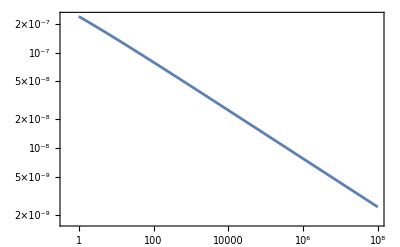

```mathematica
Show[{
ListLogLogPlot[ExtinctionHarvestRate,Frame->True,Joined->True](*,
LogLogPlot[λ[M],{M,1,10^7}]*)
}]
```

```mathematica
LinearModelFit[Log@ExtinctionHarvestRate,x,x]
```

FittedModel[…]

What percent of mortality is due to extinction-inducing harvest mortality? (without predation)

```mathematica
ExtinctionPercentHarvestMortality =Table[{ExtinctionHarvestRate[[i,1]],( ExtinctionHarvestRate[[i,2]]/(σ[M]*(1-RsolNoPred/kRes)+μ[M]+ExtinctionHarvestRate[[i,2]]))/.{M->ExtinctionHarvestRate[[i,1]],ξ->ExtinctionHarvestRate[[i,2]]}},{i,1,Length[ExtinctionHarvestRate],1}];
```

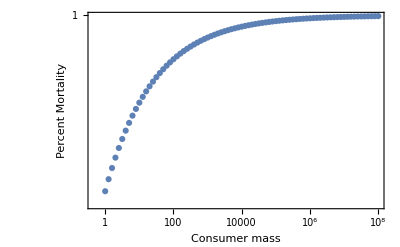

```mathematica
ListLogLogPlot[ExtinctionPercentHarvestMortality,Frame->True,PlotRange->All, FrameLabel->{"Consumer mass","Percent Mortality"}]
```

Quantify extinction-inducing harvest rate when there is also predation

```mathematica
SSHarvestWithPred = (Csol/.{ξ->x,w->1});
SSNoHarvestWithPred = (Csol/.{ξ->0,w->1});
SSHarvestWithGenPred = (Csol/.{ξ->x,w->0.37});
SSNoHarvestWithGenPred = (Csol/.{ξ->0,w->0.37});
```

```mathematica
ExtinctionHarvestRateWithPred=Table[{10^i,Select[Re[x/.NSolve[SSHarvestWithPred==0/.M->10^i,x]],#>0&][[1]]},{i,0,8,0.1}];
ExtinctionHarvestRateWithGenPred=Table[{10^i,Select[Re[x/.NSolve[SSHarvestWithGenPred==0/.M->10^i,x]],#>0&][[1]]},{i,0,8,0.1}];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ExtinctionPercentHarvestMortalityWithPred =Table[{ExtinctionHarvestRateWithPred[[i,1]],( ExtinctionHarvestRateWithPred[[i,2]]/(σ[M]*(1-(Rsol/.w->1)/kRes)+μ[M]+bP[M]+ExtinctionHarvestRateWithPred[[i,2]]))/.{M->ExtinctionHarvestRateWithPred[[i,1]],ξ->ExtinctionHarvestRateWithPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithPred],1}];
```

```mathematica
ExtinctionPercentHarvestMortalityWithGenPred =Table[{ExtinctionHarvestRateWithGenPred[[i,1]],( ExtinctionHarvestRateWithGenPred[[i,2]]/(σ[M]*(1-(Rsol/.w->0.37)/kRes)+μ[M]+(0.37)*bP[M]+ExtinctionHarvestRateWithGenPred[[i,2]]))/.{M->ExtinctionHarvestRateWithGenPred[[i,1]],ξ->ExtinctionHarvestRateWithGenPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithGenPred],1}];
```

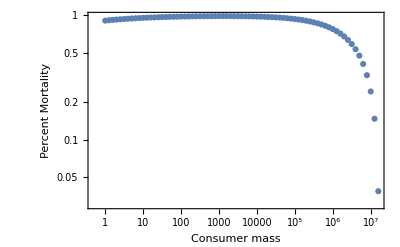

```mathematica
ListLogLogPlot[ExtinctionPercentHarvestMortalityWithGenPred,Frame->True, FrameLabel->{"Consumer mass","Percent Mortality"}]
```

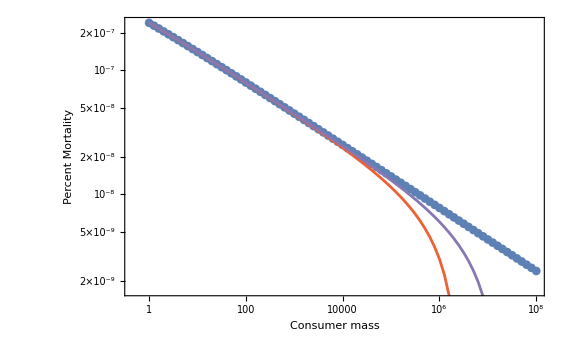

```mathematica
Show[{
ListLogLogPlot[ExtinctionHarvestRate,Frame->True, FrameLabel->{"Consumer mass","Percent Mortality"}],
ListLogLogPlot[ExtinctionHarvestRateWithPred,PlotStyle->ColorData[97,4],Frame->True,Joined->True],
ListLogLogPlot[ExtinctionHarvestRateWithGenPred,PlotStyle->ColorData[97,5],Frame->True,Joined->True]
}]
```

```mathematica
lm=LinearModelFit[Log@ExtinctionHarvestRate,x,x]
```

FittedModel[-15.2036-0.250865 x]

```mathematica
Table[ColorData[97,i],{i,1,20,1}]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.838355547812947, 0.44746667828057946, 0.0208888695323676],RGBColor[0.5833680111493557, 0.4126186601628758, 0.8290799721266107],RGBColor[0.8996399512215667, 0.7463488834690629, 0.],RGBColor[0.8439466852489265, 0.3467106629502147, 0.3309221912517893],RGBColor[0.28240003484173815, 0.6090799721266095, 0.7538800418100857]}

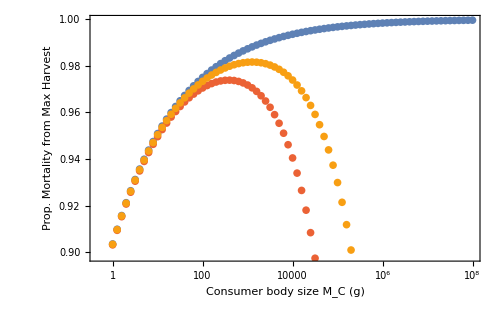

```mathematica
Show[{
ListLogLinearPlot[ExtinctionPercentHarvestMortality,Frame->True,FrameLabel->{"Consumer body size M_C (g)","Prop. Mortality from Max Harvest"},LabelStyle->Directive[FontSize->16]],
ListLogLinearPlot[ExtinctionPercentHarvestMortalityWithPred,Frame->True,PlotStyle->ColorData[97,4]],
ListLogLinearPlot[ExtinctionPercentHarvestMortalityWithGenPred,Frame->True,PlotStyle->ColorData[97,13]]
},ImageSize->500]
```

How many generations to extinction?

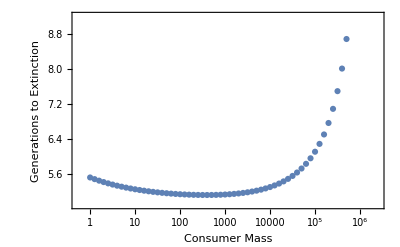

```mathematica
ListLogLinearPlot[Table[{ExtinctionHarvestRateWithPred[[i,1]],Log[0.1]/(-ξ*τLam[M])/.{M->ExtinctionHarvestRateWithPred[[i,1]],ξ->ExtinctionHarvestRateWithPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithPred],1}],
Frame->True, FrameLabel->{"Consumer Mass","Generations to Extinction"}
]
```

How many years to extinction?

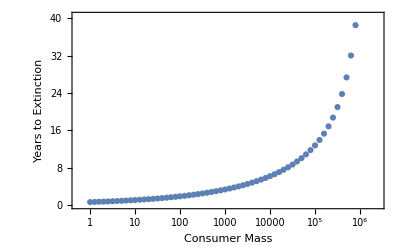

```mathematica
ListLogLinearPlot[Table[{ExtinctionHarvestRateWithPred[[i,1]],(Log[0.01]/(-ξ))*((1/60)*(1/60)*(1/24)*(1/365))/.{M->ExtinctionHarvestRateWithPred[[i,1]],ξ->ExtinctionHarvestRateWithPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithPred],1}],Frame->True, FrameLabel->{"Consumer Mass","Years to Extinction"}
]
```

```mathematica
fractionremain = 0.01;
(*Area of California*)
areaharvested =4.24*10^11;(* 2.45*10^13;*) (*meters^2*)
IndsHarvestedPerYear=Table[{ExtinctionHarvestRate[[i,1]],(SSNoHarvest*(1-fractionremain))/(M*(Log[fractionremain]/(-ξ)))*(60*60*24*365)*(areaharvested)}/.{M->ExtinctionHarvestRate[[i,1]],ξ->ExtinctionHarvestRate[[i,2]]},{i,1,Length[ExtinctionHarvestRate],1}];
IndsHarvestedPerYearPred=Table[{ExtinctionHarvestRateWithPred[[i,1]],(SSNoHarvestWithPred*(1-fractionremain))/(M*(Log[fractionremain]/(-ξ)))*(60*60*24*365)*(areaharvested)}/.{M->ExtinctionHarvestRateWithPred[[i,1]],ξ->ExtinctionHarvestRateWithPred[[i,2]]},{i,1,Length[ExtinctionHarvestRateWithPred],1}];
IndsHarvestedPerYearGenPred=Table[{ExtinctionHarvestRateWithGenPred[[i,1]],(SSNoHarvestWithGenPred*(1-fractionremain))/(M*(Log[fractionremain]/(-ξ)))*(60*60*24*365)*(areaharvested)}/.{M->ExtinctionHarvestRateWithGenPred[[i,1]],ξ->ExtinctionHarvestRateWithGenPred[[i,2]]},{i,1,Length[ExtinctionHarvestRateWithGenPred],1}];
IndsHarvestedPerYearTime=Table[{ExtinctionHarvestRate[[i,1]],(Log[fractionremain]/(-ξ))*((1/60)*(1/60)*(1/24)*(1/365))/.{M->ExtinctionHarvestRate[[i,1]],ξ->ExtinctionHarvestRate[[i,2]]}},{i,1,Length[ExtinctionHarvestRate],1}];
IndsHarvestedPerYearTimeWithPred=Table[{ExtinctionHarvestRateWithPred[[i,1]],(Log[0.01]/(-ξ))*((1/60)*(1/60)*(1/24)*(1/365))/.{M->ExtinctionHarvestRateWithPred[[i,1]],ξ->ExtinctionHarvestRateWithPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithPred],1}];
IndsHarvestedPerYearTimeWithGenPred=Table[{ExtinctionHarvestRateWithGenPred[[i,1]],(Log[0.01]/(-ξ))*((1/60)*(1/60)*(1/24)*(1/365))/.{M->ExtinctionHarvestRateWithGenPred[[i,1]],ξ->ExtinctionHarvestRateWithGenPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithGenPred],1}];
```

```mathematica
(*Set Harvest Size to be that of an elephant/mammoth*)
HarvestedSize = (2.5)*10^6;
```

```mathematica
HarvestedPosition=Position[Abs[IndsHarvestedPerYear[[All,1]]-HarvestedSize],Min[Abs[IndsHarvestedPerYear[[All,1]]-HarvestedSize]]][[1]][[1]];
```

From Fordham et al. 2021 and Alroy 2001

CC is in grams/m^2 and time is in seconds
Cmax (grams/m^2) = 1.875*10^-6

```mathematica
AlroySol =  DSolve[CC'[t]==-(NN*s*F*CC[t])/(G + CC[t]/(Cmax*M)),CC[t],t]
AlroyTime=Solve[ϵ*Cstart==CC[t]/.AlroySol[[1]],t]/.C[1]->Cstart
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{CC[t]→Cmax G M ProductLog[ⅇ^(-(F NN s t)/G+C[1]/(Cmax G M))/(Cmax G M)]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(Cstart-Cmax G M Log[Cstart ⅇ^((Cstart ϵ)/(Cmax G M)) ϵ])/(Cmax F M NN s)}}

Individuals harvested per meter^2 per second
We can either calculate it from

```mathematica
AlroyHarvestedtoextinction = ((1/M)*(Cstart-ϵ*Cstart))/(t/.AlroyTime[[1]])
```

(Cmax F NN s (Cstart-Cstart ϵ))/(Cstart-Cmax G M Log[Cstart ⅇ^((Cstart ϵ)/(Cmax G M)) ϵ])

Individuals harvested per year in area the size of California

```mathematica
AlroyAnnualharvest=AlroyHarvestedtoextinction*(60*60*24*365)*A
```

(31536000 A Cmax F NN s (Cstart-Cstart ϵ))/(Cstart-Cmax G M Log[Cstart ⅇ^((Cstart ϵ)/(Cmax G M)) ϵ])

Individuals harvested per year in area the size of California

```mathematica
PredictedStart = SSNoHarvest/.{ϵ->0,M->HarvestedSize*2.4}
```

0.724243

```mathematica
annualharvestCA = Flatten[Table[{χF,χN,AlroyAnnualharvest}/.{M->HarvestedSize*2.4,Cmax->1.875*10^-6,G->0.4,NN->1*(1+χN),s->7.884*10^-8,ϵ->fractionremain,A->areaharvested,Cstart->PredictedStart,F->0.35*(1+χF)},{χF,-0.9,0,0.01},{χN,-0.9,0,0.01}],1];
annualharvestTimeCA = Flatten[Table[{χF,χN,(t/.AlroyTime[[1]])*(1/(60*60*24*365))}/.{M->HarvestedSize*2.4,Cmax->1.875*10^-6,G->0.4,NN->1*(1+χN),s->7.884*10^-8,ϵ->fractionremain,A->areaharvested,Cstart->PredictedStart,F->0.35*(1+χF)},{χF,-0.9,0,0.01},{χN,-0.9,0,0.01}],1];
```

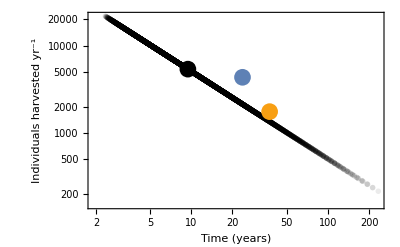

```mathematica
Show[{
ListLogLogPlot[Transpose[{annualharvestTimeCA[[All,3]],annualharvestCA[[All,3]]}],Frame->True,FrameLabel->{"Time (years)","Individuals harvested yr^-1"},LabelStyle->Directive[FontSize->16],PlotRange->All,PlotStyle->Directive[{PointSize[0.01],Opacity[0.08],Black,Point}]],
Graphics[{PointSize[0.03],Black,Point[{Log@(Median[annualharvestTimeCA[[All,3]]]),Log@(Median[annualharvestCA[[All,3]]])}]}],
Graphics[{PointSize[0.03],ColorData[97,1],Point[{Log@IndsHarvestedPerYearTime[[HarvestedPosition,2]],Log@IndsHarvestedPerYear[[HarvestedPosition,2]]}]}],
Graphics[{PointSize[0.03],ColorData[97,13],Point[{Log@IndsHarvestedPerYearTimeWithGenPred[[HarvestedPosition,2]],Log@IndsHarvestedPerYearGenPred[[HarvestedPosition,2]]}]}]
(*,
Graphics[{Thin,Line[{{Log@(2*10^6),Log@Min[Re[annualharvestCA[[All,3]]]]},{Log@(2*10^6),Log@Max[Re[annualharvestCA[[All,3]]]]}}]}]*)
},ImageSize->400]
```

Elephant Trade Calculations

```mathematica
Volume1810=(0.1*1000)*(1*10^3); (*VolumeofTrade in tonnes * 1*10^3 kg per tonne*)
Volume1980 =( 0.95*1000)*(1*10^3);
TuskMass1810=15; (*grams*)
TuskMass1980 = 5;
TusksPerElephant = 1.88;
areaAfrica =3.22122*10^12;(* 3.036*10^13;*) (*meters^2*) (*2.434*10^13*)
areaSubSahAfrica = 2.434*10^13;
ElephantsHarvestedPerYear1810 = Volume1810*1/TuskMass1810*1/TusksPerElephant*areaharvested/areaAfrica
ElephantsHarvestedPerYear1980= Volume1980*1/TuskMass1980*1/TusksPerElephant*areaharvested/areaAfrica
```

466.763

13302.7

```mathematica
linelegend = LineLegend[{ColorData[97,1],ColorData[97,13],ColorData[97,4]},{"w=0.00","w=0.37","w=1.00"}]
pointlegend = PointLegend[{Black,ColorData[97,3],ColorData[97,18]},{"Mammuthus","Diprotodon","Loxodonta"},LegendMarkerSize->20]
```

```mathematica
linelegendraster = Rasterize[linelegend,RasterSize->500]
pointlegendraster = Rasterize[pointlegend,RasterSize->500]
```

-Graphics-

-Graphics-

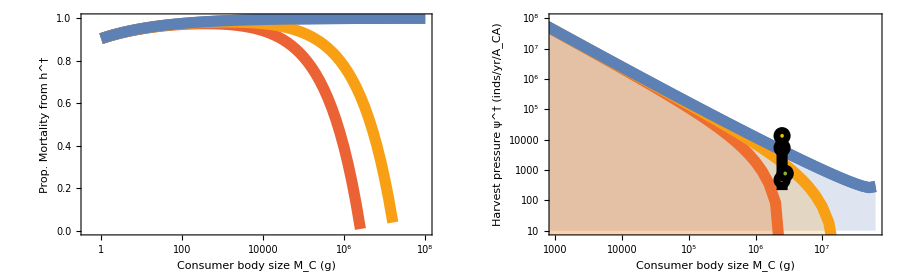

```mathematica
HarvestPlot=GraphicsRow[{
Show[{
ListLogLinearPlot[ExtinctionPercentHarvestMortality,PlotRange->{{All,10^8},{0,1}},Frame->True,FrameLabel->{"Consumer body size M_C (g)","Prop. Mortality from h^†"},LabelStyle->Directive[FontSize->16],PlotStyle->Directive[{Thickness[0.01],ColorData[97,1]}],Joined->True(*,Filling->Bottom*)],
ListLogLinearPlot[ExtinctionPercentHarvestMortalityWithPred,Frame->True,PlotStyle->Directive[{Thickness[0.01],ColorData[97,4]}],Joined->True(*,Filling->Bottom*)],
ListLogLinearPlot[ExtinctionPercentHarvestMortalityWithGenPred,Frame->True,PlotStyle->Directive[{Thickness[0.01],ColorData[97,13]}],Joined->True(*,Filling->Bottom*)],
ListLogLinearPlot[ExtinctionPercentHarvestMortality,Frame->True,PlotStyle->Directive[{Thickness[0.01],ColorData[97,1]}],Joined->True(*,Filling->Bottom*)],
Graphics[Inset[linelegendraster,{Log@3,0.2}]]
},ImageSize->800],
Show[{
ListLogLogPlot[IndsHarvestedPerYear,PlotRange->{{1000,All},{10,10^8}},Frame->True,FrameLabel->{"Consumer body size M_C (g)","Harvest pressure ψ^† (inds/yr/A_CA)"},LabelStyle->Directive[FontSize->16],PlotStyle->Directive[{Thickness[0.01],ColorData[97,1]}],Joined->True,Filling->Bottom],
ListLogLogPlot[IndsHarvestedPerYearPred,PlotStyle->Directive[{Thickness[0.01],ColorData[97,4]}],Joined->True,Filling->Bottom],
ListLogLogPlot[IndsHarvestedPerYearGenPred,PlotStyle->Directive[{Thickness[0.01],ColorData[97,13]}],Joined->True,Filling->Bottom],
ListLogLogPlot[IndsHarvestedPerYear,PlotStyle->Directive[{Thickness[0.01],ColorData[97,1]}],Joined->True,Filling->None],
DiskSize={0.18,0.41};
(*Show[{*)

Graphics[{Thickness[0.01],Black,Line[{{Log@(HarvestedSize),Log@Min[Re[annualharvestCA[[All,3]]]]},{Log@(HarvestedSize),Log@Max[Re[annualharvestCA[[All,3]]]]}}]}],
Graphics[{EdgeForm[{Black,Thickness[0.006],Opacity[1]}],FaceForm[Black],Disk[{Log@(HarvestedSize),Log@(Median[annualharvestCA[[All,3]]])},DiskSize]}],
Graphics[{EdgeForm[{Black,Thickness[0.006],Opacity[1]}],FaceForm[ColorData[97,18]],Disk[{Log@(HarvestedSize),Log@(ElephantsHarvestedPerYear1810)},DiskSize]}],
Graphics[{EdgeForm[{Black,Thickness[0.006],Opacity[1]}],FaceForm[ColorData[97,18]],Disk[{Log@(HarvestedSize),Log@(ElephantsHarvestedPerYear1980)},DiskSize]}],
(*Graphics[{Thick,ColorData[97,3],Line[{{Log@(2.786*10^6),Log@(678.4)},{Log@(2.786*10^6),Log@(848)}}]}],*)
Graphics[{EdgeForm[{Black,Thickness[0.006],Opacity[1]}],FaceForm[ColorData[97,3]],Disk[{Log@(2.786*10^6),Log@(Mean[{678.4,848}])},DiskSize]}],
Graphics[Inset[pointlegendraster,{Log@(10^7),Log@(10^6.5)}]]
(*}]*)
},ImageSize->800]
},Spacings->Scaled[0],ImageSize->900]
```

```mathematica
Export[StringJoin[{"[YOUR FILE PATH]/fig_harvest.pdf"}],HarvestPlot,"PDF"];
```

```mathematica
Median[annualharvestCA[[All,3]]]
```

5373.71

```mathematica
Mean[{678.4,848}]
```

763.2

```mathematica
ElephantsHarvestedPerYear1810
```

466.763

```mathematica
ElephantsHarvestedPerYear1980
```

13302.7